# Clearing Variables

This section just clears all the variables that have been already defined in Mathematica

```mathematica
Quiet@Remove["Global`*"]
```

# Parameters

This section is to set all the parameters of the system, including tolerances and parameters that are set to indicate Mathematica what wants to be computed

```mathematica
tol=10^-9; (*Tolerance for the initial conditions to compute the bifurcation curves*)
Choptol=10^-9; (*A number that is lower than this tolerance in absolute value will be considered as zero*)
disttol=10^-6; (*If two points are closer than this distance to each other, they will be considered the same point*)
nmax=5; (*Order of the expansion. Available choices are 3 and 5. If higher than five, the computation will take longer and the other coefficients will not be used.*)
initialt=-1000;
finalt=1000; (*These two parameters set the interval for the parameter that defines the curve such that initialt<=time<=finalt*)
smalldifferential=0.001; (*Threshold to stop the computation when the curve goes away from the rectangle if further away from this distance*)
curvespeed=1; (*Speed of the curve in the sense that ||x'(t)||=curvespeed for every value of t.*)
numberofzerotemporalderivatives=0; (*In some cases, some time derivatives are equal to zero. In that case, this number indicated the number of those derivatives that are zero. See the Swift-Hohenberg example*)
eqbool=1; (*If 1, then Mathematica computes the homogeneous steady states of the system and you can take one of those. If 0, then Mathematica will search for any bifurcation curve for any homogeneous steady state*)
simpleeq=1; (*1 if the expression of the steady state is "simple" so that it can be replaced in the formulas that determine the bifurcation, 0 otherwise*)
criticalitychanges="y"; (*"y" if you want Mathematica to find changes of criticality, "n" otherwise.*)
timedifference=1; (*This is the time step-size for finding codimension-two bifurcation points*)
cod2="n"; (*"y" if you want to continue any of the codimension-two points considering a third parameter, "n" otherwise.*)
crosscoef="n"; (*"y" if you want to compute the cross-order coefficient, "n" otherwise.*)
alphaval="n"; (*"y" if you want to compute the alpha coefficients in the normal form, "n" otherwise*)
var={u,v}; (*Names of the variables of the system*)
par={α,c}; (*Parameters you want to plot the bifurcation diagram with respect to, in the order {x, y}*)
parnames={}; (*In case Mathematica has a problem with a parameter name you want to use, you can change the parameter names in the previous variable and set the "right" name of it here.*)
crosspar={c}; (*Parameter to compute the cross-order coefficient, if crosscoef="y"*)
parval={α->2,c->10}; (*Parameter values at a bifurcation point. If they are not known, Mathematica will compute everything assuming that a specific submatrix (n - 1)x(n - 1) of the Jacobian matrix is invertible.*)
fixedpar={δ->0.1}; (*Values of the parameters that will be fixed throughout the computation*)
initialvalueTuring={{α,2}}; (*Lines to search. Mathematica will take the values of parameters in this variable, it will fix them and will find all the Turing bifurcation curves in that line with respect to the other parameter*)
intervalx={0,5}; (*Range of values of the parameter in the x axis*)
intervaly={0,50}; (*Range of values of the parameter in the y axis*)
par3={}; (*Parameters to use to continue codimension-two points, in the order {x, y, z}. Two of the parameters must be the ones in the variable par*)
par3name={}; (*In case Mathematica has a problem with the third parameter name you want to use, you can change the parameter name in the previous variable and set the "right" name of it here.*)
extrainterval={}; (*Range of values of the third parameter in the z axis*)
otherTuring={}; (*Values of the thirs parameter that get fixed tocompute the Turing bifurcation curve at each of those fixed values*)
```

# Kinetics

Provide the kinetics and the diffusion matrix in this section on the variables “kinetics” and “diffmatrix”, respectively. In this section, Mathematica will also find the homogeneous steady states if requested

```mathematica
SetDirectory[NotebookDirectory[]];
nvar=Length[var];
kinetics={α/δ-c*u+u^2*v,(c-1)*u-u^2*v}; (*Kinetics of the system*)
diffmatrix=DiagonalMatrix[{δ^2,1}]; (*Diffusion matrix*)
If[eqbool==1,
eqs=Solve[kinetics==0,var];
If[Length[eqs]>1,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Your system has " <> ToString[Length[eqs]] <> " equilibria"}],"Output"]];
For[eqnum=1,eqnum<=Length[eqs],eqnum++,
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Equilibrium number " <> ToString[eqnum] <> " is equal to ",ToString[eqs[[eqnum]],FormatType->StandardForm]}],"Output"]];];
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
NotebookClose[aux];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;
];
,
Print["Mathematica found only one homogeneous steady-state in your system. It will proceed with that one."];
eq=eqs[[1]]//Simplify;
]
,
eq={0};
]
jacmat=D[kinetics,{var}];
```

Mathematica found only one homogeneous steady-state in your system. It will proceed with that one.

# Kernel of the Jacobian matrix

Mathematica finds the kernel of the Jacobian matrix, after finding an invertible (n - 1)x(n - 1) submatrix on it, if the parameters for a bifurcation were provided.

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix;
zerodet=Det[dummymat];
zerodet=zerodet/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]]-λNF*IdentityMatrix[nvar][[row,col]],{row,nvar},{col,nvar}]];
nonzero=D[zerodet,λNF]/.λNF->0;
zerodet=zerodet/.λNF->0;
zeroder=D[zerodet,μNF];
If[Length[eq]>1,
μval=Quiet@Solve[zeroder==0/.eq/.fixedpar/.parval,μNF];
For[solnum=1,solnum<=Length[μval],solnum++,
If[Chop[μNF/.μval[[solnum]],Choptol]∈Reals && Abs[zerodet]<tol/.μval[[solnum]]/.eq/.fixedpar/.parval,
μval=μval[[solnum]];
Break[]
];
If[i==Length[μval],
Print["You are not actually at a Turing bifurcation"]];
]
];
ϕ=Table[Subscript[v, varnum],{varnum,nvar}];
If[ValueQ[μval] && Length[μval[[1]]]==0,
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]
];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.eq/.fixedpar/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
]
]
,
criticalrow=1;
criticalcol=1;
submatrixrows=Complement[Range[nvar],{criticalrow}];
submatrixcols=Complement[Range[nvar],{criticalcol}];
];
ϕ[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕ[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕ[[submatrixcols]]][[1]];
ϕ=ϕ/.ϕsol;
For[varnum=1,varnum<=nvar,varnum++,
If[varnum<=nvar-numberofzerotemporalderivatives,
ϕ[[varnum]]=ϕ[[varnum]];
,
ϕ[[varnum]]=0;
]
]
Subscript[sol, 1,1]=Table[Subscript[W, 1,1,varnum][X]->Subscript[A, 1][X]*ϕ[[varnum]],{varnum,nvar}];
Subscript[dersol, 1,1]=D[Subscript[sol, 1,1],X];
Subscript[der2sol, 1,1]=D[Subscript[dersol, 1,1],X];
```

# Kernel of the adjoint

Mathematica finds the kernel of the transpose of the Jacobian matrix, using the same submatrix used before.

```mathematica
ψ=Table[Subscript[v, varnum],{varnum,nvar}];
ψ[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψ[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψ[[submatrixrows]]][[1]];
ψ=ψ/.ψsol;
```

# Bifurcation curves

Mathematica finds the bifurcation curves satisfying all the constraints imposed by the kinetics and the Turing conditions. To do that, it solves an initial value problem starting at a bifurcation point found using the lines to search defined above.

```mathematica
If[Length[par]==2,
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,nvar}];
kineticsaux=kinetics/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence;
zerodetaux=zerodet/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence;
zeroderaux=zeroder/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+μNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
equationsGlobalLP=Append[kineticsaux,zerodetaux/.μNF[time]->0];
equationsGlobalLP=D[equationsGlobalLP,time];
AppendTo[equationsGlobalLP,(par[[1]]'[time])^2+(par[[2]]'[time])^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equationsGlobalLP=Table[equationsGlobalLP[[equationnumber]]==0,{equationnumber,Length[equationsGlobalLP]}];
allvar=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
AppendTo[allvar,μNF];
allvartimedependent=Table[allvar[[nvar]][time],{nvar,Length[allvar]}];
allvarGlobalLP=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvarGlobalLP,par[[1]]];
AppendTo[allvarGlobalLP,par[[2]]];
allvarGlobalLPtimedependent=Table[allvarGlobalLP[[nvar]][time],{nvar,Length[allvarGlobalLP]}];
numberofbifurcationcurves=Length[initialvalueTuring];
solutioncurves={};
solutioncurvesGlobalLP={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[Length[eq]==1 || simpleeq==0,
initialvalues=Quiet@NSolve[Join[{zerodet,zeroder},kinetics]==0/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]],μNF},var]//Evaluate];
initialvaluesGlobalLP=Quiet@NSolve[Join[{zerodet},kinetics]==0/.fixedpar/.μNF->0/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]]},var]//Evaluate];
,
initialvalues=Quiet@NSolve[{zerodet,zeroder}==0/.eq/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]],μNF}//Evaluate];
initialvaluesGlobalLP=Quiet@NSolve[zerodet==0/.μNF->0/.eq/.fixedpar/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],par[[anotherparameter]]//Evaluate];
];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet @ If[¬(var∈Reals)/.eq/.fixedpar/.initialvalues[[initialsolnum]],Continue[]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.fixedpar/.initialvalues[[initialsolnum]]),{varnum,nvar}]]
];
If[Activate[Inactivate[Chop[μNF,Choptol]!=0 &&
Max[Abs[{zerodet,zeroder}]]<tol && If[Length[eq]>1,Norm[(var/.eq)-var]<tol,True] && If[anotherparameter==1,intervalx[[1]],intervaly[[1]]]<=par[[anotherparameter]]<=If[anotherparameter==1,intervalx[[2]],intervaly[[2]]] && Chop[nonzero,Choptol]!=0/.fixedpar/.initialvalues[[initialsolnum]]]],
dereval=Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]->initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]==initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==intervalx[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==intervalx[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==intervaly[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==intervaly[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
tempsol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[tempsol]>0&& tempsol[[1]][[1]][[2]]["Domain"][[1]][[1]]<tempsol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves,tempsol];
]
]
]
];
initialvaluesGlobalLP=Table[Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]]->Re[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}],{initialsolnum,Length[initialvaluesGlobalLP]}];
initialvaluesGlobalLP=DeleteDuplicates[initialvaluesGlobalLP];
For[initialsolnum=1,initialsolnum<=Length[initialvaluesGlobalLP],initialsolnum++,
AppendTo[initialvaluesGlobalLP[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet@If[¬(var∈Reals)/.eq/.fixedpar/.initialvaluesGlobalLP[[initialsolnum]],Continue[]];
initialvaluesGlobalLP[[initialsolnum]]=Join[initialvaluesGlobalLP[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.fixedpar/.initialvaluesGlobalLP[[initialsolnum]]),{varnum,nvar}]]
];
If[Activate[Inactivate[Abs[zerodet/.μNF->0]<tol && If[Length[eq]>1,Norm[(var/.eq)-var]<tol,True] && If[anotherparameter==1,intervalx[[1]],intervaly[[1]]]<=par[[anotherparameter]]<=If[anotherparameter==1,intervalx[[2]],intervaly[[2]]]]/.fixedpar/.initialvaluesGlobalLP[[initialsolnum]]],
dereval=Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]->initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equationsGlobalLP/.time->0/.dereval,D[allvarGlobalLPtimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equationsGlobalLP,Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]==initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==intervalx[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==intervalx[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==intervaly[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==intervaly[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
tempsol=Quiet@NDSolve[equationsaux,allvarGlobalLP,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[tempsol]>0 && tempsol[[1]][[1]][[2]]["Domain"][[1]][[1]]<tempsol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurvesGlobalLP,tempsol];
]
]
]
]
];
If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"This script could not find a Turing bifurcation curve or a BD-line for your desired parameters. Try changing tolerances or initial values"}],"Output"]]]
]
```

# Auxiliary variables

If the third and/or fifth-order coefficients were already found and saved, this section only loads the corresponding files. Otherwise, this section defines the variables to make the Taylor expansion of the system

```mathematica
coefs="y";
If[nmax>=5,
If[FileExistsQ["Third-order coefficient.mx"] && FileExistsQ["Fifth-order coefficient.mx"],
C3=Import["Third-order coefficient.mx"];
C5=Import["Fifth-order coefficient.mx"];
coefs="n";
];
,
If[FileExistsQ["Third-order coefficient.mx"],
C3=Import["Third-order coefficient.mx"];
coefs="n";
]
]
If[coefs=="y",
conjpar={Conjugate[y_]->y};
Subscript[sol, 0,0]=Table[Subscript[W, 0,0,varnum][X]->var[[varnum]],{varnum,nvar}];;
Subscript[dersol, 0,0]=D[Subscript[sol, 0,0],X];
Subscript[der2sol, 0,0]=D[Subscript[dersol, 0,0],X];
For[order=1,order<=5,order++,
For[sub=0,sub<=5,sub++,
If[(EvenQ[order]&& ¬EvenQ[sub]) || (¬EvenQ[order] && EvenQ[sub]),
Subscript[sol, order,sub]=Table[Subscript[W, order,sub,varnum][X]->0,{varnum,nvar}];
Subscript[dersol, order,sub]=D[Subscript[sol, order,sub],X];
Subscript[der2sol, order,sub]=D[Subscript[dersol, order,sub],X];
]
]
];
jacobianmat=jacobianmat/.μNF->kNF^2;
jacobianmatr=jacmat-mul^2*μNF*diffmatrix/.μNF->kNF^2;
ϕ=ϕ/.μNF->kNF^2;
ψ=ψ/.μNF->kNF^2;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μNF->kNF^2;
Subscript[dersol, 1,1]=Subscript[dersol, 1,1]/.μNF->kNF^2;
Subscript[der2sol, 1,1]=Subscript[der2sol, 1,1]/.μNF->kNF^2;
conjprime={Conjugate'[y_]->HoldForm[Conjugate[D[y,X]]/D[y,X]]};
absprime={Abs'[y_]->HoldForm[(D[y,X]*Conjugate[y]+y*Conjugate[D[y,X]])/(2*D[y,X]*Abs[y])]};
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order][x,X]->∑_(sub=-order)^order Subscript[W, order,sub,varnum][X] ⅇ^(ⅈ sub kNF x)/.Table[Subscript[W, order,-index,varnum][X]->Conjugate[Subscript[W, order,index,varnum][X]],{index,order}],{order,0,nmax},{varnum,nvar}]]/. Subscript[sol, 1,0]/. Subscript[sol, 2,1]/. Subscript[sol, 3,0]/. Subscript[sol, 3,2]/. Subscript[sol, 4,1]/. Subscript[sol, 4,3];
toexpandderxx=Flatten[Table[D[Subscript[var⟦varnum⟧, order][x,X],x,x]->-kNF^2∑_(sub=-order)^order sub^2*Subscript[W, order,sub,varnum][X] ⅇ^(ⅈ sub kNF x)/.Table[Subscript[W, order,-index,varnum][X]->Conjugate[Subscript[W, order,index,varnum][X]],{index,order}],{order,0,nmax},{varnum,nvar}]]/. Subscript[sol, 1,0]/. Subscript[sol, 2,1]/. Subscript[sol, 3,0]/. Subscript[sol, 3,2]/. Subscript[sol, 4,1]/. Subscript[sol, 4,3];
toexpandderXx=Flatten[Table[D[Subscript[var⟦varnum⟧, order][x,X],X,x]->ⅈ*kNF∑_(sub=-order)^order sub*Subscript[W, order,sub,varnum]'[X] ⅇ^(ⅈ sub kNF x)/.Table[Subscript[W, order,-index,varnum]'[X]->Conjugate[Subscript[W, order,index,varnum]'[X]],{index,order}],{order,0,nmax},{varnum,nvar}]]/. Subscript[dersol, 1,0]/. Subscript[dersol, 2,1]/. Subscript[dersol, 3,0]/. Subscript[dersol, 3,2]/. Subscript[dersol, 4,1]/. Subscript[dersol, 4,3];
toexpandderXX=Flatten[Table[D[Subscript[var⟦varnum⟧, order][x,X],X,X]->∑_(sub=-order)^order Subscript[W, order,sub,varnum]''[X] ⅇ^(ⅈ sub kNF x)/.Table[Subscript[W, order,-index,varnum]''[X]->Conjugate[Subscript[W, order,index,varnum]''[X]],{index,order}],{order,0,nmax},{varnum,nvar}]]/. Subscript[der2sol, 1,0]/. Subscript[der2sol, 2,1]/. Subscript[der2sol, 3,0]/. Subscript[der2sol, 3,2]/. Subscript[der2sol, 4,1]/. Subscript[der2sol, 4,3];
]
```

# Taylor expansion

Mathematica computes the Taylor expansion of the system up to order nmax

```mathematica
If[coefs=="y",
expr=kinetics/.Table[var[[varnum]]->∑_(order=0)^nmax ϵNF^order*Subscript[var[[varnum]], order][x,X],{varnum,nvar}];
expansion={};
For[order=1,order<=nmax,order++,
AppendTo[expansion,1/(order!)D[expr,{ϵNF,order}]/.ϵNF->0];
]
]
```

# Ansatz expansion

Addition of the linear operator to the expansion of the reaction

```mathematica
If[coefs=="y",
equations={};
For[order=1,order<=nmax,order++,
If[order<=2,
AppendTo[equations,expansion[[order]]+Dot[diffmatrix,Table[D[Subscript[var[[varnum]], order][x,X], x,x],{varnum,nvar}]]];
,
If[3<=order<=4,
AppendTo[equations,expansion[[order]]+Dot[diffmatrix,Table[D[Subscript[var[[varnum]], order][x,X], x,x],{varnum,nvar}]+2*Table[D[Subscript[var[[varnum]], order-2][x,X], x,X],{varnum,nvar}]]];
,
AppendTo[equations,expansion[[order]]+Dot[diffmatrix,Table[D[Subscript[var[[varnum]], order][x,X], x,x],{varnum,nvar}]+2*Table[D[Subscript[var[[varnum]], order-2][x,X], x,X],{varnum,nvar}]+Table[D[Subscript[var[[varnum]], order-4][x,X], X,X],{varnum,nvar}]]];
]
]
]
]
```

# Solving equations at each order

Mathematica solves the equation at each order to find the symbolic coefficients

```mathematica
If[coefs=="y",
solvcond={};
AppendTo[solvcond,0];
For[order=2,order<=nmax,order++,
If[EvenQ[order],
AppendTo[solvcond,0];
];
equation=equations[[order]]/.toexpand/.toexpandderxx/.toexpandderXx/.toexpandderXX;
For[sub=0,sub<=order,sub++,
If[(EvenQ[order]&& ¬ EvenQ[sub]) || (¬ EvenQ[order] && EvenQ[sub]),
Continue[]
];
If[order==nmax && sub!=1,
Continue[]
];
If[order==4 && sub>2,
Continue[]
];
auxeq=kNF/(2π)∫_0^((2π)/kNF) equation*ⅇ^(-ⅈ*sub*kNF*x)ⅆx//Simplify;
auxeq=-auxeq/.Table[Subscript[W, order,sub,varnum][X]->0,{varnum,nvar}]//Simplify;
If[order!=1,
If[sub!=1,
auxsol=LinearSolve[dummymat,dummyvec];
auxsol=auxsol/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.mul->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
Subscript[sol, order,sub]=Table[Subscript[W, order,sub,varnum][X]->auxsol[[varnum]],{varnum,nvar}];
,
AppendTo[solvcond,-Dot[auxeq,ψ]/Dot[ϕ,ψ]];
If[order!=nmax,
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
auxsol=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
auxsol=auxsol/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
usefulvec[[submatrixcols]]=Table[Subscript[W, order,sub,submatrixcols[[varnum]]][X]->auxsol[[varnum]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[W, order,sub,criticalcol][X]->0;
Subscript[sol, order,sub]=usefulvec;
]
];
Subscript[dersol, order,sub]=ReleaseHold[ReleaseHold[D[Subscript[sol, order,sub],X]/.conjprime]/.absprime];
Subscript[der2sol, order,sub]=ReleaseHold[ReleaseHold[D[Subscript[dersol, order,sub],X]/.conjprime]/.absprime];
]
]
]
]
```

# Getting coefficients

Mathematica extracts the third and fifth-order coefficients from the previous expansion.Also, Mathematica finds the coefficients α_i that determine the equation the amplitude solves at a codimension-two point

```mathematica
If[coefs=="y",
C3=solvcond[[3]];
For[order=2,order>=0,order--,
For[sub=0,sub<=order,sub++,
C3 = C3/. Subscript[sol, order,sub]/. Subscript[dersol, order,sub]/. Subscript[der2sol, order,sub];
]
];
C3=C3/.Subscript[A, 1]'[X]->0/.Subscript[A, 1][X]->1/.conjpar;
Export["Third-order coefficient.mx",C3];
If[nmax>=5,
C5=solvcond[[5]];
For[order=4,order>=0,order--,
For[sub=0,sub<=order,sub++,
If[order==4 && sub>2,
Continue[]
];
C5=C5/. Subscript[sol, order,sub]/. Subscript[dersol, order,sub]/. Subscript[der2sol, order,sub];
]
];
If[alphaval=="y",
C5=FunctionExpand[C5];
Subscript[αNF, 1]=C5/.Subscript[A, 1][X]->0/.Subscript[A, 1]''[X]->1/.conjpar;
C5=C5/.Subscript[A, 1]''[X]->0;
Subscript[αNF, 2]=-ⅈ*(Coefficient[C5/.Conjugate[Subscript[A, 1]'[X]]->0,Subscript[A, 1]'[X]]/.Subscript[A, 1][X]->1)/.conjpar;
Subscript[αNF, 3]=-ⅈ*Coefficient[C5,Conjugate[Subscript[A, 1]'[X]]]/.Subscript[A, 1][X]->1/.conjpar;
C5=C5/.Subscript[A, 1]'[X]->0/.Subscript[A, 1][X]->1/.conjpar;
Export["alpha1.mx",Subscript[αNF, 1]];
Export["alpha2.mx",Subscript[αNF, 2]];
Export["alpha3.mx",Subscript[αNF, 3]];
,
C5=C5/.Subscript[A, 1]''[X]->0/.Subscript[A, 1]'[X]->0/.Subscript[A, 1][X]->1/.conjpar;
];
Export["Fifth-order coefficient.mx",C5];
]
]
```

# Cross-order coefficient

Mathematica finds the cross-order coefficient, if requested

```mathematica
If[crosscoef=="y" && Length[eq]>1,
If[Length[crosspar]==1,
crosspar=crosspar[[1]];
];
C11=Dot[Dot[D[jacobianmat/.eq,crosspar],ϕ],ψ]/Dot[ϕ,ψ];
]
```

# Changes of criticality

Mathematica finds the changes of criticality if requested

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
If[nmax>=5,
fifthcoeff={};
];
If[criticalitychanges!="y",
Throw["You do not want to find changes of criticality"];
];
codimensiontwopoints={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
aux=Join[{par[[1]][time],par[[2]][time],μNF[time]},var]/.variabledependence;
If[Variables[aux/.solutioncurves[[outersolnum]][[innersolnum]]/.time->0]!={},Continue[]];
auxC3=Compile[{time},#,RuntimeOptions->{"EvaluateSymbolically"->False}]&@ (C3/.fixedpar/.kNF->√μNF/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
allvals=Table[{time,auxC3[time]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
vals={};
For[valnum=1,valnum<=Length[allvals]-1,valnum++,
If[allvals[[valnum]][[2]]*allvals[[valnum+1]][[2]]<0 && allvals[[valnum]][[1]]>solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]] && Chop[μNF[allvals[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0,
AppendTo[vals,allvals[[valnum]][[1]]]
]
];
For[tnum=1,tnum<=Length[vals],tnum++,
initialvalueoft=vals[[tnum]];
critchangetemp=time/.Quiet@FindRoot[auxC3[time],{time,initialvalueoft}];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[auxC3[critchangetemp]]<tol && (μNF[critchangetemp]/.solutioncurves[[outersolnum]][[innersolnum]])>0,
auxiliaryarray=Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),μNF->(μNF[time]/.solutioncurves[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp;
AppendTo[codimensiontwopoints,auxiliaryarray];
If[ValueQ[fifthcoeff],
AppendTo[fifthcoeff,{{par[[1]][time],par[[2]][time]}/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,{C5/.fixedpar/.kNF->√μNF/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp}}];
Break[]
]
]
]
]
];
If[Length[codimensiontwopoints]>0,
codimensiontwopoints=Join[{par[[1]],par[[2]],μNF},var]/.codimensiontwopoints;
codimensiontwopoints=DeleteDuplicates[codimensiontwopoints,EuclideanDistance[##]<disttol&];
critchange=Table[{par[[1]]->codimensiontwopoints[[critnum]][[1]],par[[2]]->codimensiontwopoints[[critnum]][[2]]},{critnum,Length[codimensiontwopoints]}];
codimensiontwopoints=Table[Join[{par[[1]]->codimensiontwopoints[[critnum]][[1]],par[[2]]->codimensiontwopoints[[critnum]][[2]],μNF->codimensiontwopoints[[critnum]][[3]]},Table[var[[varnum]]->codimensiontwopoints[[critnum]][[3+varnum]],{varnum,nvar}]],{critnum,Length[codimensiontwopoints]}];
If[ValueQ[fifthcoeff],
auxarr={};
For[critnum=1,critnum<=Length[critchange],critnum++,
getout=0;
For[fifthnum=1,fifthnum<=Length[fifthcoeff],fifthnum++,
If[getout==0 && fifthcoeff[[fifthnum]][[1]]=={par[[1]],par[[2]]}/.critchange[[critnum]],
AppendTo[auxarr,fifthcoeff[[fifthnum]]];
getout=1;
]
]
];
fifthcoeff=auxarr;
];
If[ValueQ[fifthcoeff] && Length[fifthcoeff]>0,Export["Fifth-order coefficient at codimension-two bifurcation points.txt",fifthcoeff];
,
If[ValueQ[critchange] && Length[critchange]>0,Export["Codimension-two bifurcation points.txt",critchange]];
]
]
]
]
```

# Bifurcation diagram plotting

Mathematica plots the bifurcation curves found colored according to the sign of the third order coefficient and the sign of k^2

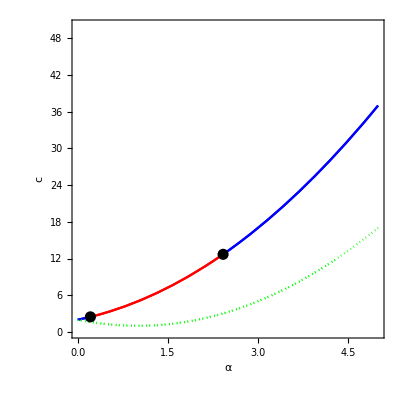

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
If[Length[parnames]<2,
parnames=par;
];
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]]]}],{critnum,Length[critchange]}];
];
bifcurveplot={};
GlobalLPplot={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
aux=Join[{par[[1]][time],par[[2]][time],μNF[time]},var]/.variabledependence;
If[Variables[aux/.solutioncurves[[outersolnum]][[innersolnum]]/.time->0]!={},Continue[]];
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.fixedpar/.kNF->√μNF/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.μNF->μNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[{If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]>0 && Chop[auxC3[time],Choptol]∈Reals && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]>0 && Chop[auxC3[time],Choptol]∈Reals && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],
If[μNF[time]==0/.solutioncurves[[outersolnum]][[innersolnum]] ,{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Red,Blue,{Green,Dotted},Gray},PlotRange->{{intervalx[[1]],intervalx[[2]]},{intervaly[[1]],intervaly[[2]]}}];
AppendTo[bifcurveplot,tempplot];
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurvesGlobalLP],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurvesGlobalLP[[outersolnum]]],innersolnum++,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalLP[[outersolnum]][[innersolnum]],{time,solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Gray},PlotRange->{{intervalx[[1]],intervalx[[2]]},{intervaly[[1]],intervaly[[2]]}}];
AppendTo[GlobalLPplot,tempplot];
]
];
bifcurveplot=Join[bifcurveplot,GlobalLPplot];
CreateDocument[Dynamic[plot2],WindowSize->{500,500}];
If[ValueQ[critpoints],
plot2=Show[bifcurveplot,critpoints,Frame->True,FrameLabel->{ToString[parnames[[1]],StandardForm],ToString[parnames[[2]],StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1] 
,
plot2=Show[bifcurveplot,Frame->True,FrameLabel->{ToString[parnames[[1]],StandardForm],ToString[parnames[[2]],StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
]
]
```

# 3D bifurcation curves

Mathematica continues codimension-two curves, if requested

```mathematica
checker=1;
If[¬ValueQ[critchange] || Length[critchange]==0 || cod2!="y",
checker=0;
]
If[checker==1,
lowerbound=Range[3];
upperbound=Range[3];
otherpar={};
For[parnum=1,parnum<=3,parnum++,
If[MemberQ[par,par3[[parnum]]],
For[index=1,index<=2,index++,
If[par3[[parnum]]==par[[index]],
If[index==1,
lowerbound[[parnum]]=intervalx[[1]];
upperbound[[parnum]]=intervalx[[2]];
,
lowerbound[[parnum]]=intervaly[[1]];
upperbound[[parnum]]=intervaly[[2]];
];
AppendTo[otherpar,parnum];
Break[]
]
]
,
lowerbound[[parnum]]=extrainterval[[1]];
upperbound[[parnum]]=extrainterval[[2]];
fixedparameter3=parnum;
]
];
parval3=parval;
For[parnum=1,parnum<=Length[fixedpar],parnum++,
If[par3[[fixedparameter3]]==fixedpar[[parnum]][[1]],
AppendTo[parval3,fixedpar[[parnum]]];
incond=fixedpar[[parnum]];
]
];
fixedpar3=Complement[fixedpar,{parval3[[-1]]}];
conjprime3={Conjugate'[y_]->HoldForm[Conjugate[D[y,time]]/D[y,time]]};
absprime3={Abs'[y_]->HoldForm[(D[y,time]*Conjugate[y]+y*Conjugate[D[y,time]])/(2*D[y,time]*Abs[y])]};
kineticsaux=kinetics/.fixedpar3/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence;
zerodetaux=zerodet/.fixedpar3/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence;
zeroderaux=zeroder/.fixedpar3/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence;
auxC3=C3/.fixedpar3/.kNF->√μNF/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
AppendTo[equations,auxC3];
equations=ReleaseHold[D[equations,time]/.conjprime3/.absprime3];
AppendTo[equations,(par3[[1]]'[time])^2+(par3[[2]]'[time])^2+(par3[[3]]'[time])^2+μNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
allvar=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvar,par3[[1]]];
AppendTo[allvar,par3[[2]]];
AppendTo[allvar,par3[[3]]];
AppendTo[allvar,μNF];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
initialconditions={};
If[Length[codimensiontwopoints]==1,
AppendTo[initialconditions,codimensiontwopoints[[1]]];
,
For[pointnum=1,pointnum<=Length[codimensiontwopoints],pointnum++,
inp=HoldForm[Input["Would you like to continue point " <> ToString[codimensiontwopoints[[pointnum]][[;;2]]] <> "[y/n]"]];
If[inp=="y",
AppendTo[initialconditions,codimensiontwopoints[[pointnum]]];
]
]
];
solutioncurves3={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
initialvalues=initialconditions[[bifnum]];
AppendTo[initialvalues,incond];
dereval=Table[initialvalues[[varnum]][[1]][0]->initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[varnum]][[1]][0]==initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par3[[fixedparameter3]][time]==extrainterval[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[fixedparameter3]][time]==extrainterval[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[1]]]][time]==lowerbound[[otherpar[[1]]]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[1]]]][time]==upperbound[[otherpar[[1]]]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[2]]]][time]==lowerbound[[otherpar[[2]]]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[2]]]][time]==upperbound[[otherpar[[2]]]]+smalldifferential//Evaluate,"StopIntegration"]];
tempsol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[tempsol]>0 && tempsol[[1]][[1]][[2]]["Domain"][[1]][[1]]<tempsol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves3,tempsol];
]
]
];
If[Length[solutioncurves3]==0,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"This script could not find a Codimension-two bifurcation curve for your desired parameters. Try changing tolerances or initial values"}],"Output"]];
]
]
```

# Other Turing bifurcation curves

As for the continuation of codimension two curves, an extra parameter is needed, this section computes more Turing bifurcation curves when that parameter is fixed at the parameter values provided above. The initial conditions considered are the codimension-two points found for that fixed parameter value in the previous cell

```mathematica
If[checker==1,
fixedparametervalues={};
initialconditions={};
turingbifurcationcurves={};
For[turingnumber=1,turingnumber<=Length[otherTuring],turingnumber++,
AppendTo[fixedparametervalues,par3[[fixedparameter3]]->otherTuring[[turingnumber]]];
];
For[turingnumber=1,turingnumber<=Length[otherTuring],turingnumber++,
getout=0;
For[outersolnum=1,outersolnum<=Length[solutioncurves3],outersolnum++,
If[getout==1,Break[]];
For[innersolnum=1,innersolnum<=Length[solutioncurves3[[outersolnum]]],innersolnum++,
solt=Quiet@NMinimize[(par3[[fixedparameter3]][time]-fixedparametervalues[[turingnumber]][[2]])^2/.solutioncurves3[[outersolnum]][[innersolnum]],time];
If[solutioncurves3[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=(time/.solt[[2]])<=solutioncurves3[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],
If[Abs[solt[[1]]]<tol,
AppendTo[initialconditions,Check[solutioncurves3[[outersolnum]][[innersolnum]]/.solt[[2]],Null]];
initialconditions[[-1]]=Table[allvar[[varnum]]->(allvar[[varnum]][time]/.initialconditions[[-1]])/.solt[[2]],{varnum,Length[allvar]}];
getout=1;
Break[];
]
]
]
]
];
For[bifnum=1,bifnum<=Length[initialconditions],bifnum++,
fixedparametereval={par3[[fixedparameter3]]->(par3[[fixedparameter3]]/.initialconditions[[bifnum]])};
kineticsaux=kinetics/.fixedpar3/.fixedparametereval/.par3[[otherpar[[1]]]]->par3[[otherpar[[1]]]][time]/.par3[[otherpar[[2]]]]->par3[[otherpar[[2]]]][time]/.μNF->μNF[time]/.variabledependence;
zerodetaux=zerodet/.fixedpar3/.fixedparametereval/.par3[[otherpar[[1]]]]->par3[[otherpar[[1]]]][time]/.par3[[otherpar[[2]]]]->par3[[otherpar[[2]]]][time]/.μNF->μNF[time]/.variabledependence;
zeroderaux=zeroder/.fixedpar3/.fixedparametereval/.par3[[otherpar[[1]]]]->par3[[otherpar[[1]]]][time]/.par3[[otherpar[[2]]]]->par3[[otherpar[[2]]]][time]/.μNF->μNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
AppendTo[equations,par3[[fixedparameter3]][time]];
equations=D[equations,time];
AppendTo[equations,(par3[[otherpar[[1]]]]'[time])^2+(par3[[otherpar[[2]]]]'[time])^2+μNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
initialvalues=initialconditions[[bifnum]];
dereval=Table[initialvalues[[varnum]][[1]][0]->initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[varnum]][[1]][0]==initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[1]]]][time]==lowerbound[[otherpar[[1]]]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[1]]]][time]==upperbound[[otherpar[[1]]]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[2]]]][time]==lowerbound[[otherpar[[2]]]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par3[[otherpar[[2]]]][time]==upperbound[[otherpar[[2]]]]+smalldifferential//Evaluate,"StopIntegration"]];
tempsol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[tempsol]>0 && tempsol[[1]][[1]][[2]]["Domain"][[1]][[1]]<tempsol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[turingbifurcationcurves,tempsol];,
]
]
]
]
```

# Codimension-two bifurcation diagram plotting

Mathematica plots the codimension-two curve with all the other Turing bifurcation curves found in the previous cell. The intersections between the Turing curves and the codimension-two curve will also be marked.

```mathematica
If[checker==1,
parnames3={};
counter=1;
For[parnum=1,parnum<=3,parnum++,
If[MemberQ[par,par3[[parnum]]],
AppendTo[parnames3,parnames[[counter]]];
counter=counter+1;
,
If[Length[par3name]==1,
AppendTo[parnames3,par3name];
,
AppendTo[parnames3,par3[[fixedparameter3]]]
]
]
];
bifcurveplot={};
turingcurveplot={};
critpoints=Table[Graphics3D[{PointSize[0.02],Point[{par3[[1]],par3[[2]],par3[[3]]}/.initialconditions[[bifnum]]]}],{bifnum,Length[initialconditions]}];
For[outersolnum=1,outersolnum<=Length[turingbifurcationcurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[turingbifurcationcurves[[outersolnum]]],innersolnum++,
aux=Join[{par3[[1]][time],par3[[2]][time],par3[[3]][time],μNF[time]},var]/.variabledependence;
If[Variables[aux/.turingbifurcationcurves[[outersolnum]][[innersolnum]]/.time->0]!={},Continue[]];
auxnonzero=Compile[{time},#,RuntimeOptions->{"EvaluateSymbolically"->False}]&@ (nonzero/.fixedpar3/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence/.turingbifurcationcurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->{"EvaluateSymbolically"->False}]&@ (C3/.fixedpar3/.kNF->√μNF/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence/.turingbifurcationcurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot3D[{If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]>0 && Chop[auxC3[time],Choptol]∈Reals && Re[auxC3[time]]<0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par3[[1]][time],par3[[2]][time],par3[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Red,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
tempplot=Quiet@ParametricPlot3D[{If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]>0 && Chop[auxC3[time],Choptol]∈Reals && Re[auxC3[time]]>0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par3[[1]][time],par3[[2]][time],par3[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Blue,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
tempplot=Quiet@ParametricPlot3D[{If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]<0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par3[[1]][time],par3[[2]][time],par3[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Green,Dotted},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurves3],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves3[[outersolnum]]],innersolnum++,
aux=Join[{par3[[1]][time],par3[[2]][time],par3[[3]][time],μNF[time]},var]/.variabledependence;
If[Variables[aux/.solutioncurves3[[outersolnum]][[innersolnum]]/.time->0]!={},Continue[]];
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar3/.par3[[1]]->par3[[1]][time]/.par3[[2]]->par3[[2]][time]/.par3[[3]]->par3[[3]][time]/.μNF->μNF[time]/.variabledependence/.solutioncurves3[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot3D[{If[Chop[auxnonzero[time],Choptol]!=0 && μNF[time]>0/.solutioncurves3[[outersolnum]][[innersolnum]],{par3[[1]][time],par3[[2]][time],par3[[3]][time]}/. solutioncurves3[[outersolnum]][[innersolnum]]]},{time,solutioncurves3[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves3[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Black,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[bifcurveplot,tempplot];
]
];
bifcurveplot=Join[turingcurveplot,bifcurveplot];
CreateDocument[Dynamic[plot3],WindowSize->{500,500}];
If[ValueQ[critpoints],
plot3=Show[bifcurveplot,critpoints,Frame->True,AxesLabel->{ToString[parnames3[[1]],StandardForm],ToString[parnames3[[2]],StandardForm],ToString[parnames3[[3]],StandardForm]},RotateLabel->False,AxesStyle->Directive[FontSize->15],BoxRatios->{1,1,1}] 
,
plot3=Show[bifcurveplot,Frame->True,AxesLabel->{ToString[parnames3[[1]],StandardForm],ToString[parnames3[[2]],StandardForm],ToString[parnames3[[3]],StandardForm]},RotateLabel->False,AxesStyle->Directive[FontSize->15],BoxRatios->{1,1,1}]
]
]
```